# Vector Field in ℝ^2

```mathematica
a=4;
```

```mathematica
F[{x_, y_}]={-x+y, -x-y};
```

```mathematica
field=VectorPlot[F[{x, y}],{x,-1.2a,1.2a},{y,-1.2a,1.2a},
FrameLabel->{x,y},
VectorPoints->10,
VectorStyle->Arrowheads[0.03]];
```

```mathematica
xAxis=Graphics[{Text["x",{1.3a,0}],Thickness[0.01],Arrow[{{-1.2a,0},{1.2a,0}}]}];
```

```mathematica
yAxis=Graphics[{Text["y",{0,1.3a}],Thickness[0.01],Arrow[{{0,-1.2a},{0,1.2a}}]}];
```

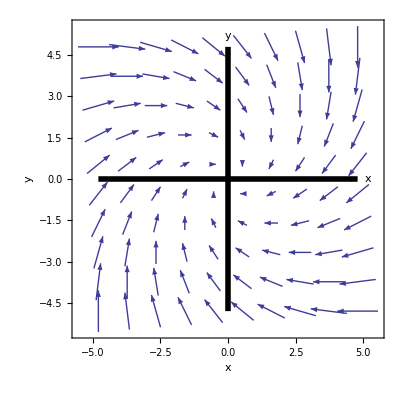

```mathematica
Show[field,xAxis,yAxis]
```